## Calculate the weights on the edge in a graph

```mathematica
EdgeWeights[g_]:=EdgeWeights[g,EdgeList[g]]
```

```mathematica
EdgeWeights[g_,edges_]:=Block[{baseSols=ChromaticPolynomial[g,4]/24, weights=Association[]},
Table[
With[{h=EdgeDelete[g,e]},
weights[e]=ChromaticPolynomial[h,4]/24-baseSols
]
,{e,edges}
];
weights
]
```

```mathematica
PaintGraph[g_]:=Block[{weights= EdgeWeights[g],maxWeight},
maxWeight = Max[Values[weights]];
Graph[
Table[
Style[UndirectedEdge[e[[1]],e[[2]]],AbsoluteThickness[5*weights[e]/maxWeight],(ColorData["DarkRainbow"][1-weights[e]/maxWeight])],{e,EdgeList[g]}]
, GraphLayout->"PlanarEmbedding",
EdgeLabels->Table[e->weights[e],{e,EdgeList[g]}],
VertexLabels->"Name",
VertexLabelStyle->Darker[Green]]
]
```

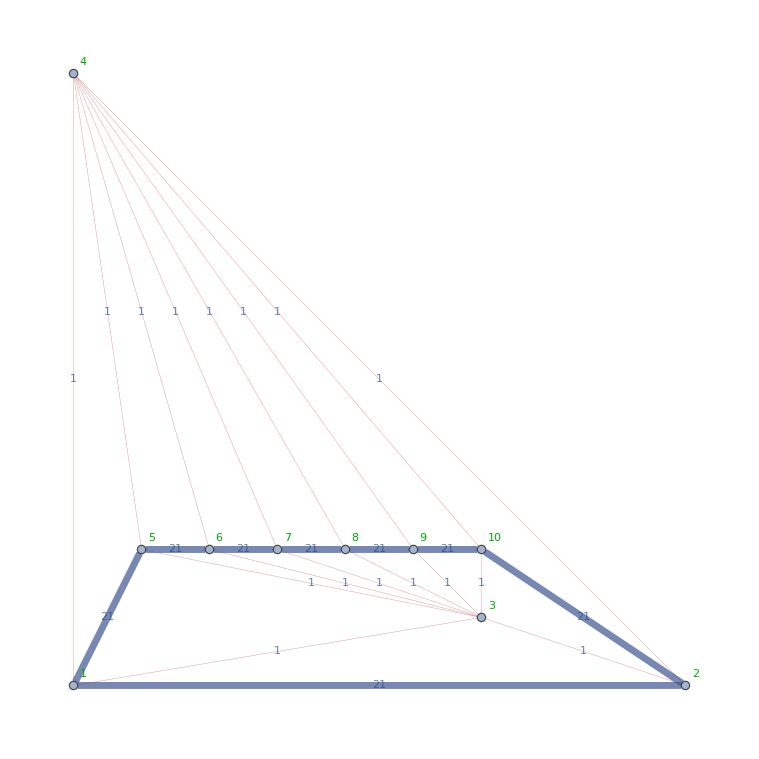

```mathematica
PaintGraph[JacobsThalGraph[6]]
```

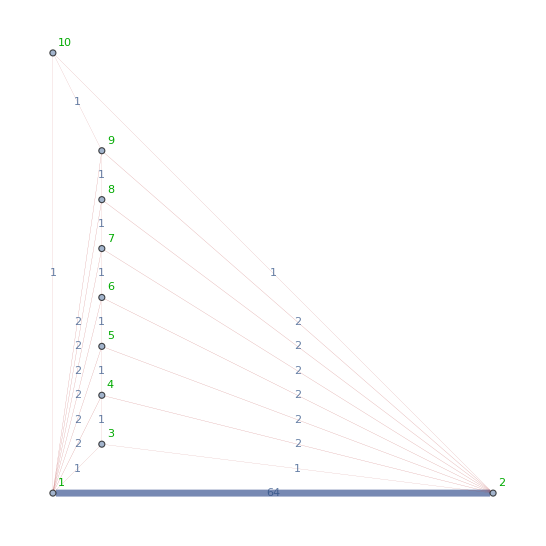

```mathematica
PaintGraph[Graph[MinimalGraph[9]]]
```

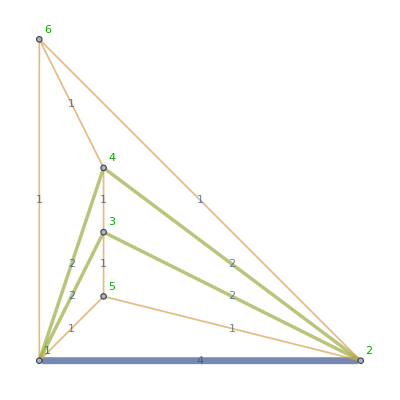
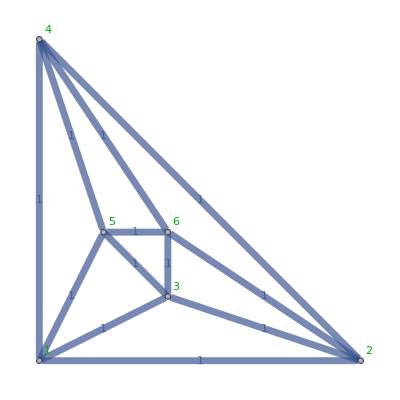
{-Graphics-,180}
{-Graphics-,15}

```mathematica
With[{all=allGraphs6,nodes=6},
Multicolumn[Tally[Table[PaintGraph[all[k,"graph"]],{k,Select[Keys[all],With[{g=all[#,"graph"]},VertexCount[g]==nodes&&MaximalPlanarQ[g]]&]}],IsomorphicGraphQ],Appearance->"Horizontal"]
]
```

```mathematica
ColorData
```

ColorData

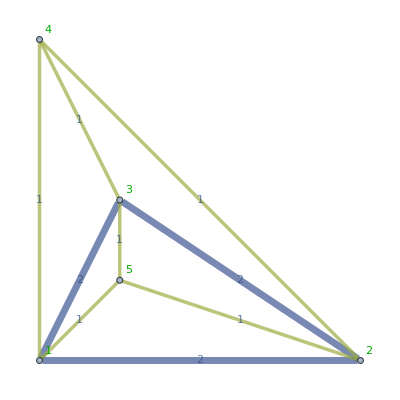
{-Graphics-,10}

```mathematica
With[{all=allGraphs5,nodes=5},
Multicolumn[Tally[Table[PaintGraph[all[k,"graph"]],{k,Select[Keys[all],With[{g=all[#,"graph"]},VertexCount[g]==nodes&&MaximalPlanarQ[g]]&]}],IsomorphicGraphQ],Appearance->"Horizontal"]
]
```

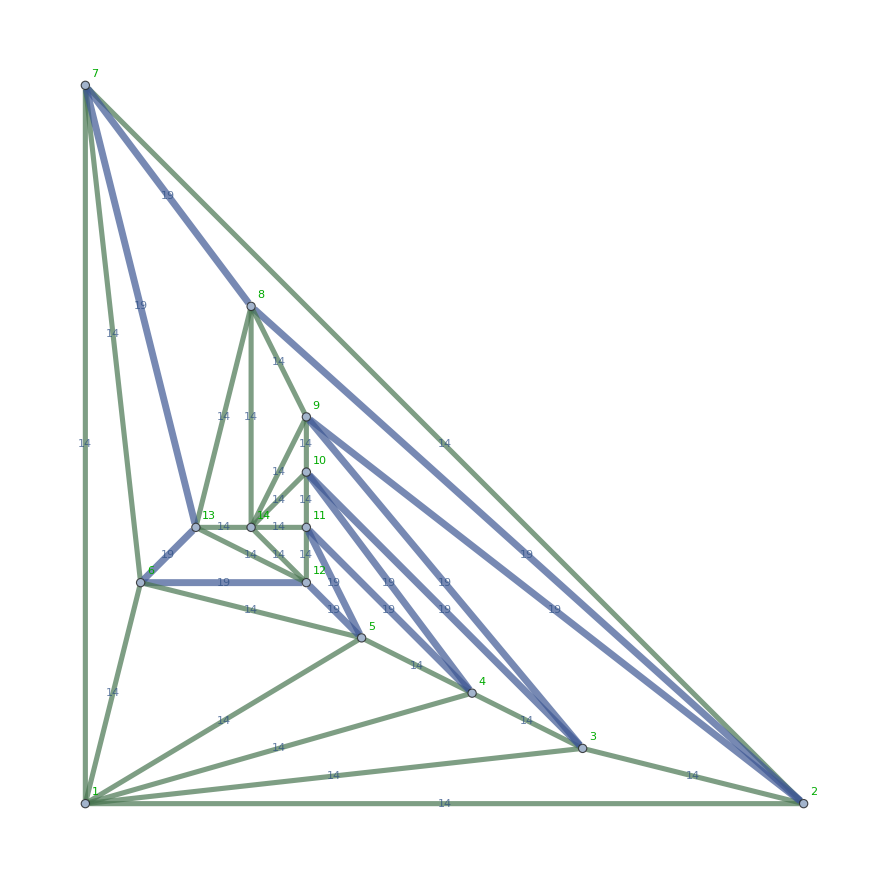

```mathematica
PaintGraph[Graph[plantri[[2]]]]
```

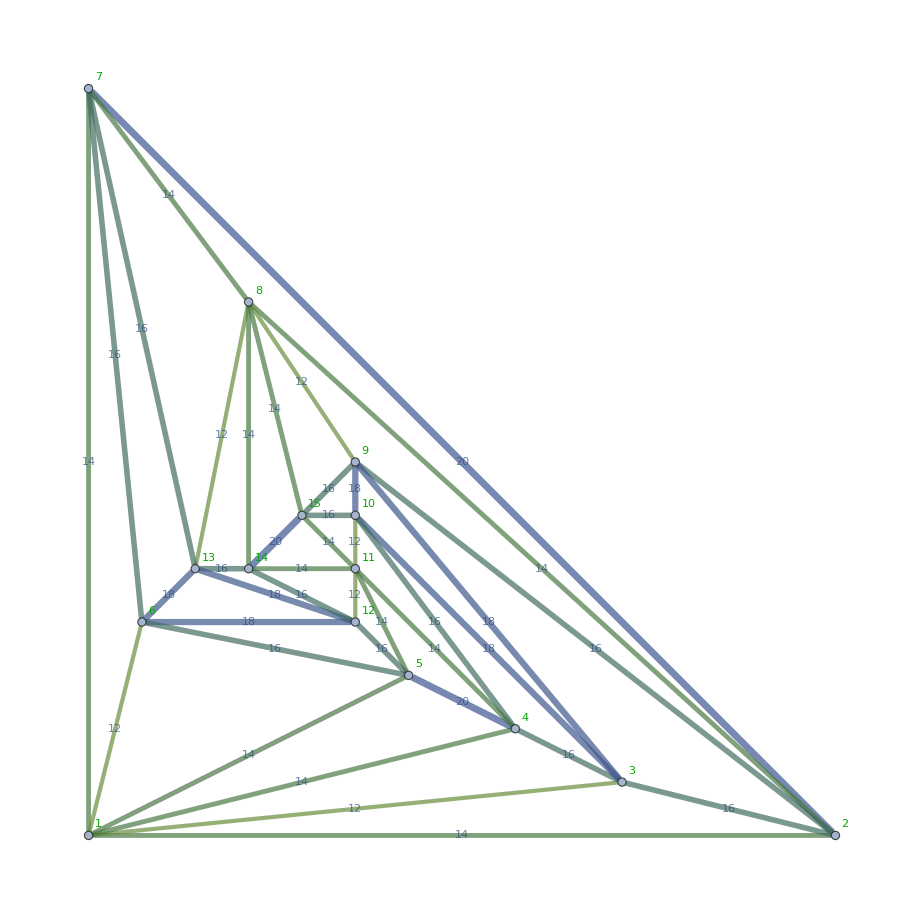

```mathematica
PaintGraph[Graph[plantri[[3]]]]
```

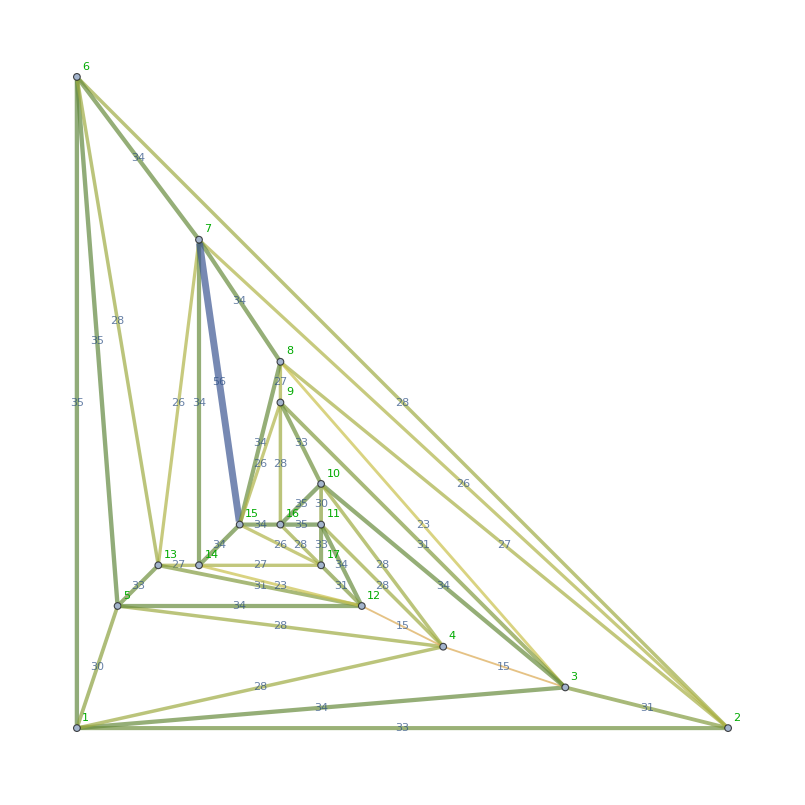

```mathematica
PaintGraph[Graph[plantri[[8]]]]
```

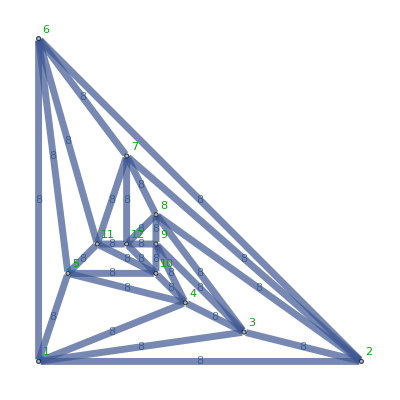
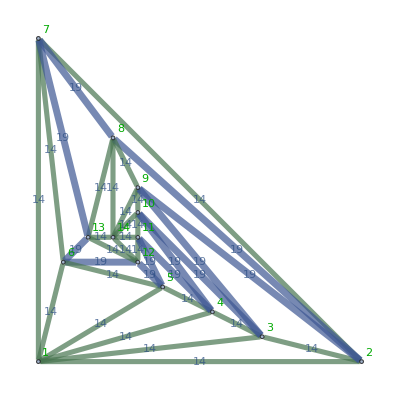
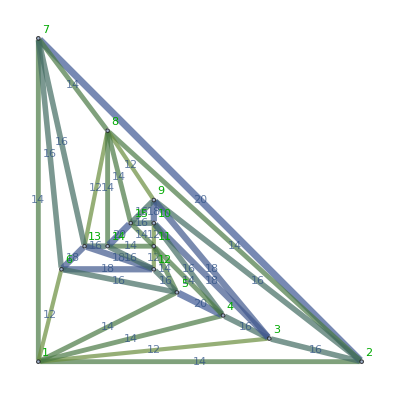
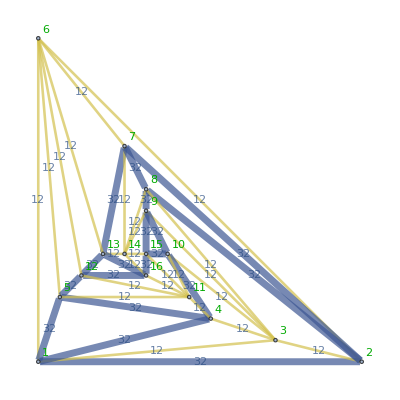
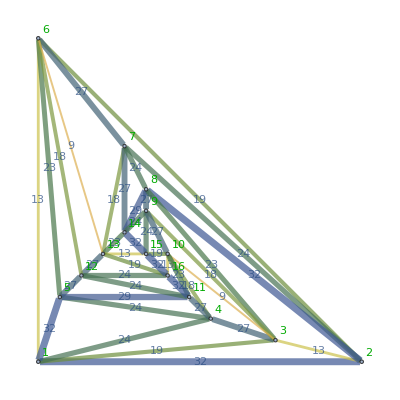
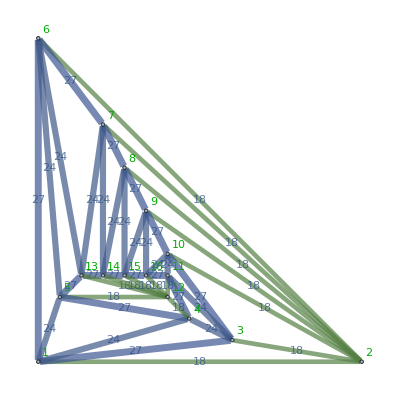
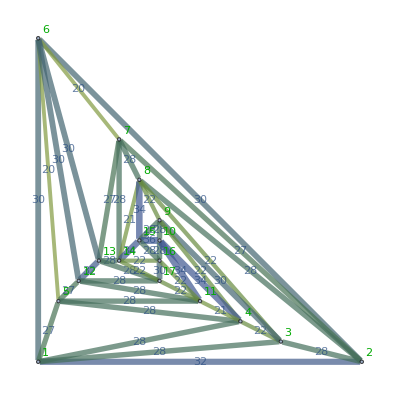
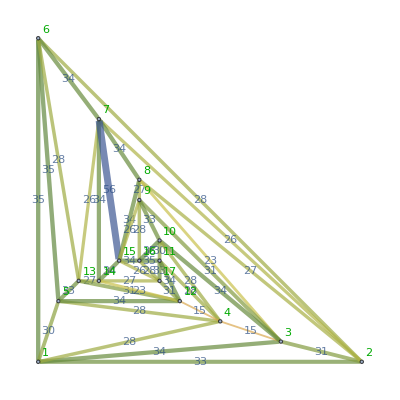

```mathematica
Table[PaintGraph[Graph[plantri[[k]]]],{k,1,10}]
```

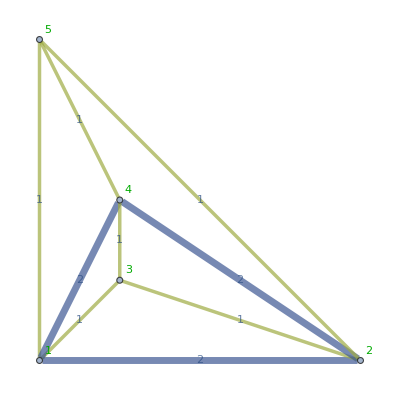
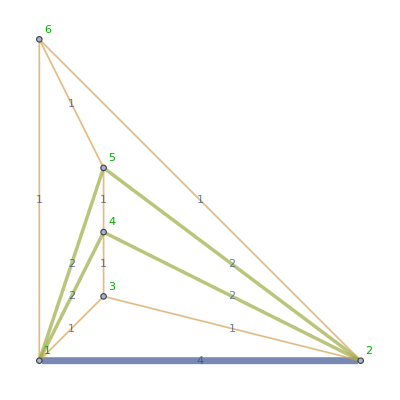
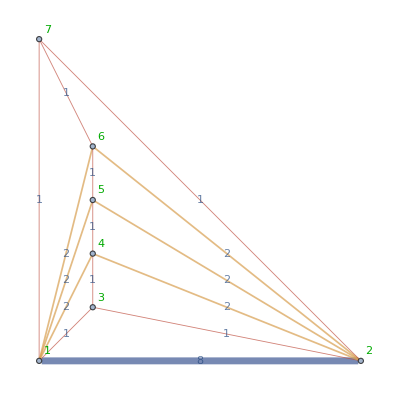
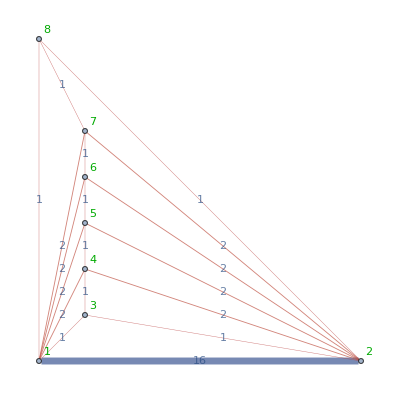
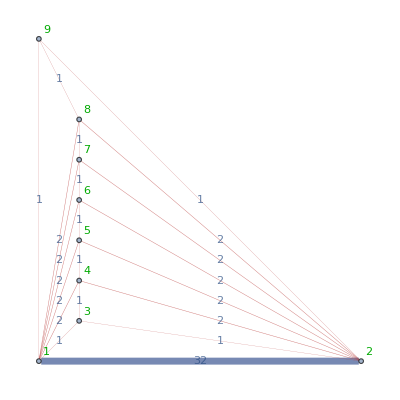
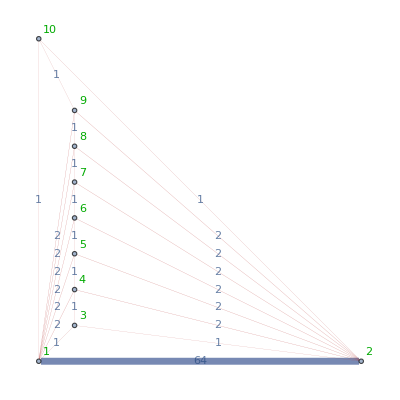
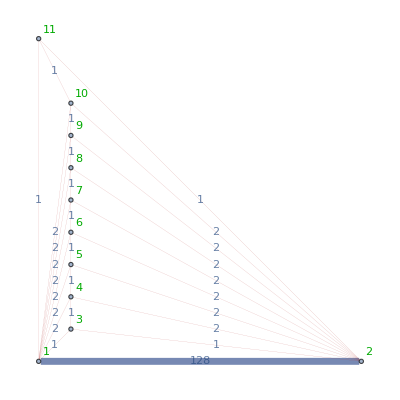
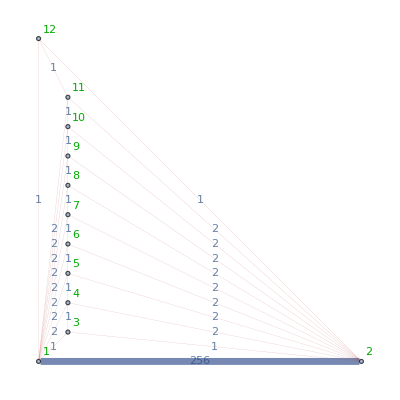

```mathematica
Table[PaintGraph[MinimalGraph[k+3]],{k,1,8}]
```

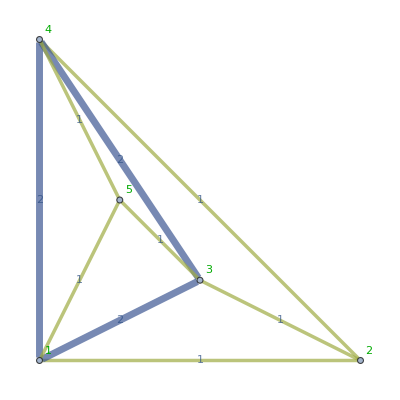
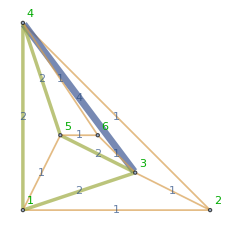
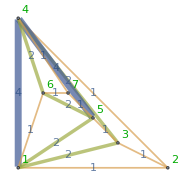
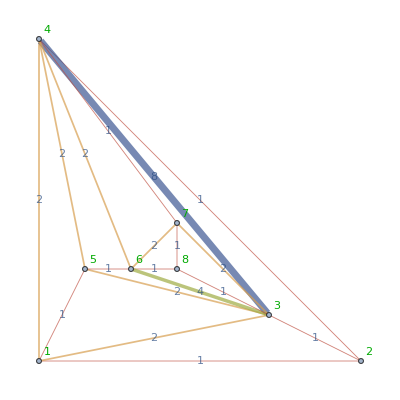
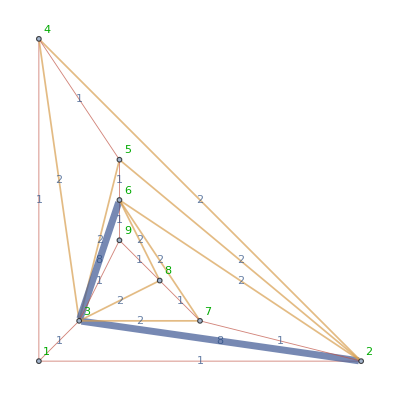
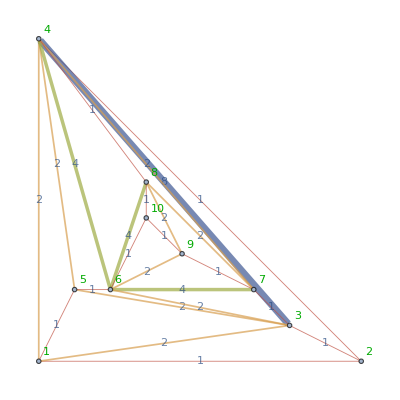
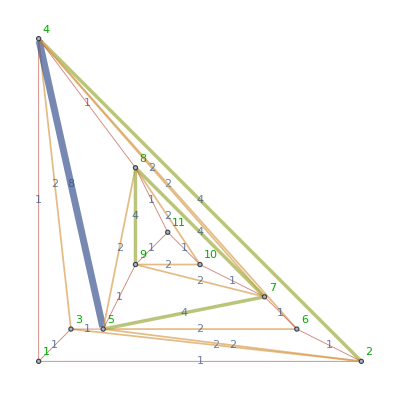
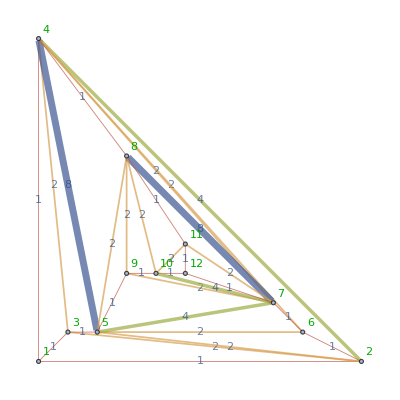

```mathematica
Table[PaintGraph[MinimalGraph2[k+3]],{k,1,8}]
```

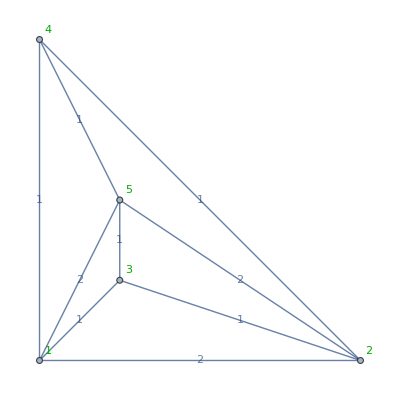
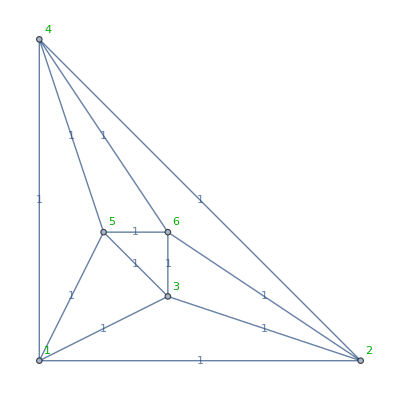
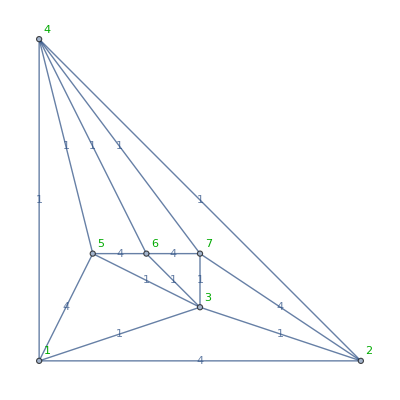
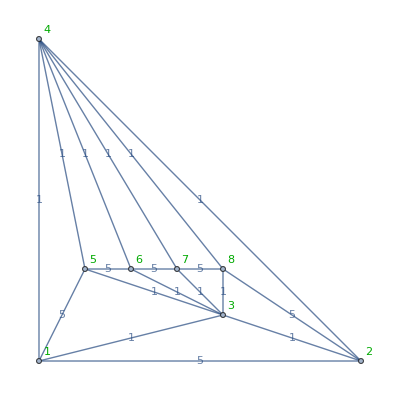
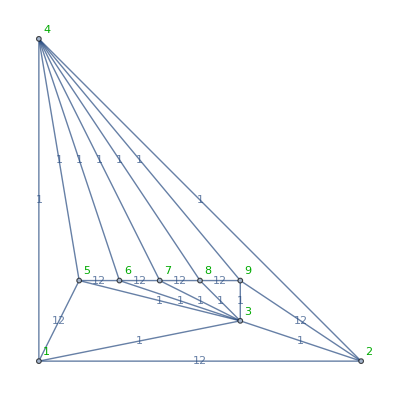
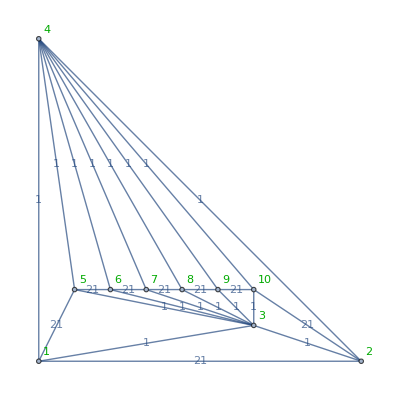
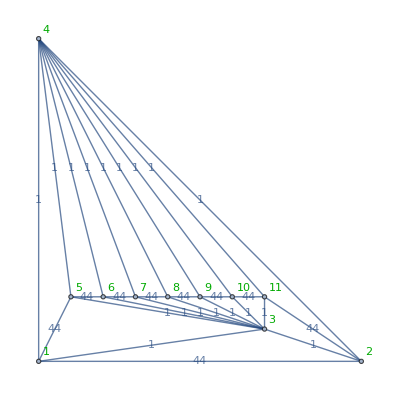
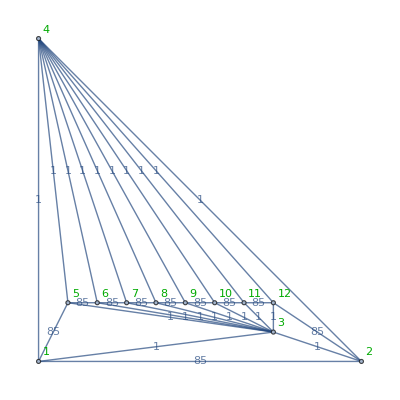
{-Graphics-1,-Graphics-4,-Graphics-5,-Graphics-12,-Graphics-21,-Graphics-44,-Graphics-85,-Graphics-172,-Graphics-341,-Graphics-684}

```mathematica
Table[With[{g=JacobsThalGraph[k]},
Labeled[PaintGraph[g],ChromaticPolynomial[g,4]/24]],{k,1,10}]
```

```mathematica
8,10,12,21,44
```

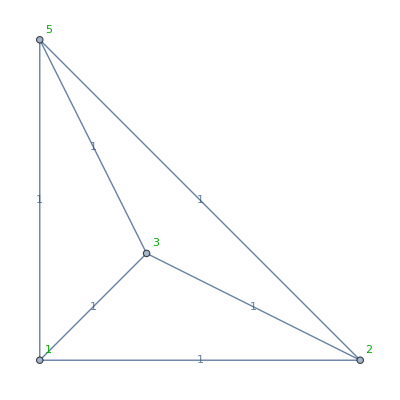
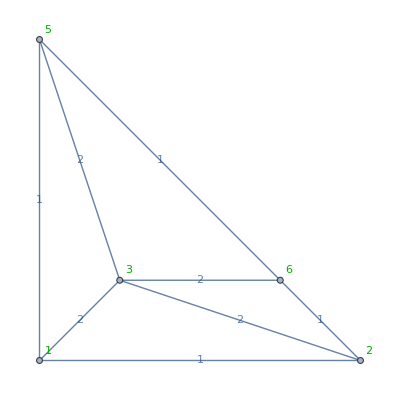
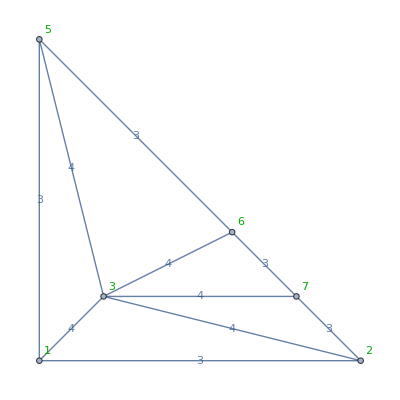
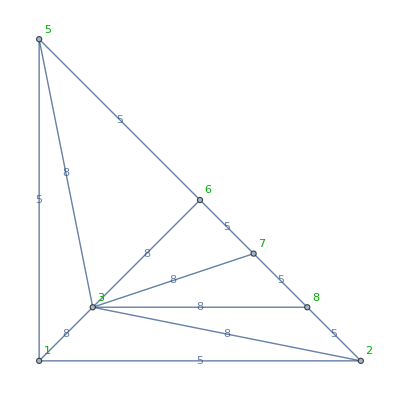
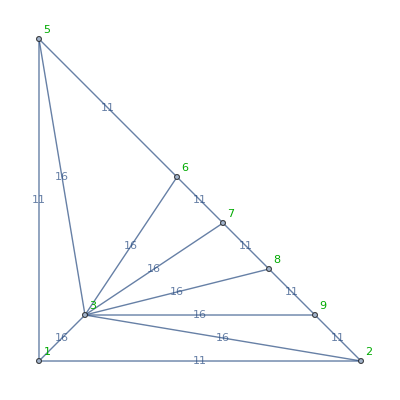
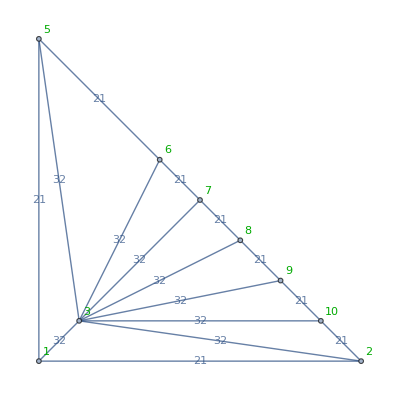
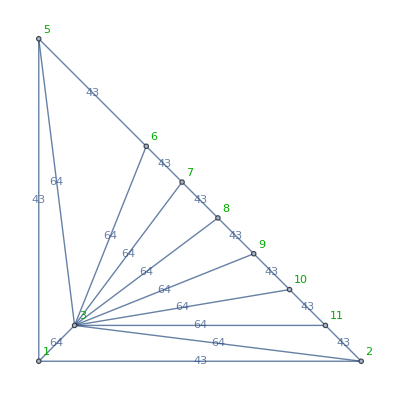
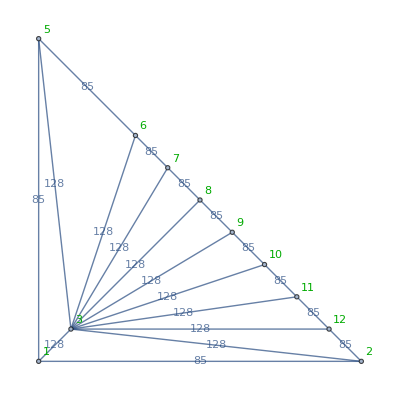
{-Graphics-1,-Graphics-3,-Graphics-5,-Graphics-11,-Graphics-21,-Graphics-43,-Graphics-85,-Graphics-171,-Graphics-341,-Graphics-683}

```mathematica
Table[With[{g=VertexDelete[JacobsThalGraph[k],4]},
Labeled[PaintGraph[g],ChromaticPolynomial[g,4]/24]],{k,1,10}]
```